### Bikin inset data w0 .33 B145 m[r]

```mathematica
input0=ReadList[FileNameJoin[{NotebookDirectory[],"TOVradmass_w0.33_B145.dat"}],{Number,Number,Number,Number,Number}];
massaTOV=Transpose[input0][[4]];
rhoTOV=Transpose[input0][[2]];
RTOV=Transpose[input0][[1]];
Dimensions[rhoTOV][[1]]
```

600

```mathematica
input1=ReadList[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha20_w0.33_B145.dat"}],{Number,Number,Number,Number,Number}];
massamod1=Transpose[input1][[4]];
rhomod1=Transpose[input1][[2]];
Rmod1=Transpose[input1][[1]];
Dimensions[rhomod1][[1]]
```

588

```mathematica
input2=ReadList[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha2_w0.33_B145.dat"}],{Number,Number,Number,Number,Number}];
massamod2=Transpose[input2][[4]];
rhomod2=Transpose[input2][[2]];
Rmod2=Transpose[input2][[1]];
Dimensions[rhomod2][[1]]
```

590

```mathematica
input3=ReadList[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e0_alpha20_w0.33_B145.dat"}],{Number,Number,Number,Number,Number}];
massamod3=Transpose[input3][[4]];
rhomod3=Transpose[input3][[2]];
Rmod3=Transpose[input3][[1]];
Dimensions[rhomod3][[1]]
```

600

```mathematica
count=Dimensions[rhoTOV][[1]]
```

600

```mathematica
dataTOV=Interpolation[Transpose[{rhoTOV,massaTOV}]]
```

InterpolatingFunction[{{233.13, 2030.13}}, <>]

```mathematica
datamod1=Interpolation[Transpose[{rhomod1,massamod1}]]
```

InterpolatingFunction[{{233.13, 2030.13}}, <>]

```mathematica
datamod2=Interpolation[Transpose[{rhomod2,massamod2}]]
```

InterpolatingFunction[{{233.13, 2030.13}}, <>]

```mathematica
datamod3=Interpolation[Transpose[{rhomod3,massamod3}]]
```

InterpolatingFunction[{{233.13, 2030.13}}, <>]

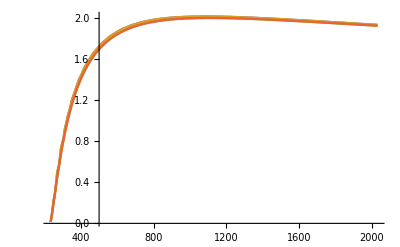

```mathematica
Plot[{datamod1[x],datamod2[x],datamod3[x],dataTOV[x]},{x,rhoTOV[[1]],rhoTOV[[count]]},PlotRange->All]
```

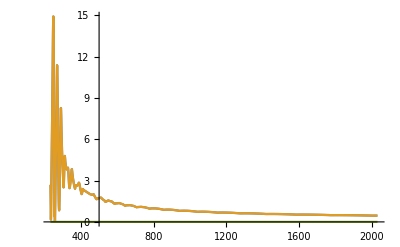

```mathematica
Plot[{100*Abs[(1-datamod1[x]/dataTOV[x])],100*Abs[(1-datamod2[x]/dataTOV[x])],100*Abs[(1-datamod3[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]]},PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha20_w0.33_B145_inset.dat"}],Table[{x,dataTOV[x],datamod1[x],100*Abs[(1-datamod1[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]],(rhoTOV[[count]]-rhoTOV[[1]])/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotRadMass\eksakradmass_lp1e-3_alpha20_w0.33_B145_inset.dat

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha2_w0.33_B145_inset.dat"}],Table[{x,dataTOV[x],datamod2[x],100*Abs[(1-datamod2[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]],(rhoTOV[[count]]-rhoTOV[[1]])/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotRadMass\eksakradmass_lp1e-3_alpha2_w0.33_B145_inset.dat

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e0_alpha20_w0.33_B145_inset.dat"}],Table[{x,dataTOV[x],datamod3[x],100*Abs[(1-datamod3[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]],(rhoTOV[[count]]-rhoTOV[[1]])/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotRadMass\eksakradmass_lp1e0_alpha20_w0.33_B145_inset.dat

### Bikin inset data w0 .33 B185 m[r]

```mathematica
input0=ReadList[FileNameJoin[{NotebookDirectory[],"TOVradmass_w0.33_B185.dat"}],{Number,Number,Number,Number,Number}];
massaTOV=Transpose[input0][[4]];
rhoTOV=Transpose[input0][[2]];
RTOV=Transpose[input0][[1]];
Dimensions[rhoTOV][[1]]
```

600

```mathematica
input1=ReadList[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha20_w0.33_B185.dat"}],{Number,Number,Number,Number,Number}];
massamod1=Transpose[input1][[4]];
rhomod1=Transpose[input1][[2]];
Rmod1=Transpose[input1][[1]];
Dimensions[rhomod1][[1]]
```

594

```mathematica
count=Dimensions[rhoTOV][[1]]
```

600

```mathematica
dataTOV=Interpolation[Transpose[{rhoTOV,massaTOV}]]
```

InterpolatingFunction[{{612.8, 2409.8}}, <>]

```mathematica
datamod1=Interpolation[Transpose[{rhomod1,massamod1}]]
```

InterpolatingFunction[{{612.8, 2409.8}}, <>]

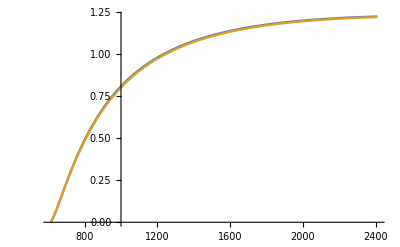

```mathematica
Plot[{datamod1[x],dataTOV[x]},{x,rhoTOV[[1]],rhoTOV[[count]]},PlotRange->All]
```

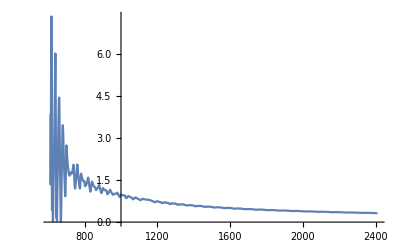

```mathematica
Plot[{100*Abs[(1-datamod1[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]]},PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha20_w0.33_B185_inset.dat"}],Table[{x,dataTOV[x],datamod1[x],100*Abs[(1-datamod1[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]],(rhoTOV[[count]]-rhoTOV[[1]])/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotRadMass\eksakradmass_lp1e-3_alpha20_w0.33_B185_inset.dat

### Bikin inset data w1 B145 m[r]

```mathematica
input0=ReadList[FileNameJoin[{NotebookDirectory[],"TOVradmass_w1_B145.dat"}],{Number,Number,Number,Number,Number}];
massaTOV=Transpose[input0][[4]];
rhoTOV=Transpose[input0][[2]];
RTOV=Transpose[input0][[1]];
Dimensions[rhoTOV][[1]]
```

600

```mathematica
input1=ReadList[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha20_w1_B145.dat"}],{Number,Number,Number,Number,Number}];
massamod1=Transpose[input1][[4]];
rhomod1=Transpose[input1][[2]];
Rmod1=Transpose[input1][[1]];
Dimensions[rhomod1][[1]]
```

560

```mathematica
count=Dimensions[rhoTOV][[1]]
```

600

```mathematica
dataTOV=Interpolation[Transpose[{rhoTOV,massaTOV}]]
```

InterpolatingFunction[{{231.13, 830.13}}, <>]

```mathematica
datamod1=Interpolation[Transpose[{rhomod1,massamod1}]]
```

InterpolatingFunction[{{231.13, 830.13}}, <>]

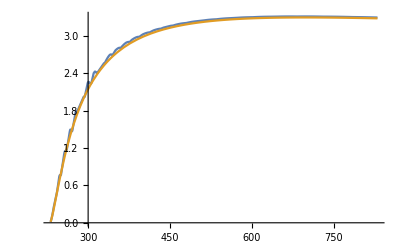

```mathematica
Plot[{datamod1[x],dataTOV[x]},{x,rhoTOV[[1]],rhoTOV[[count]]},PlotRange->All]
```

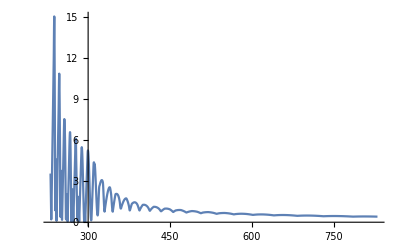

```mathematica
Plot[{100*Abs[(1-datamod1[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]]},PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"eksakradmass_lp1e-3_alpha20_w1_B145_inset.dat"}],Table[{x,dataTOV[x],datamod1[x],100*Abs[(1-datamod1[x]/dataTOV[x])]},{x,rhoTOV[[1]],rhoTOV[[count]],(rhoTOV[[count]]-rhoTOV[[1]])/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotRadMass\eksakradmass_lp1e-3_alpha20_w1_B145_inset.dat

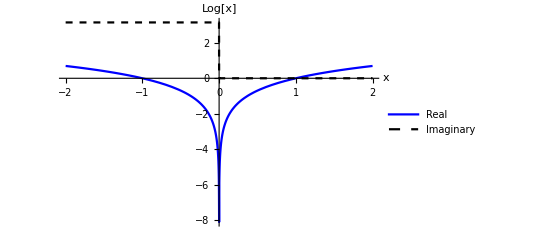

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotRadMass\log.eps

```mathematica
Plot[{Re[Log[x]],Im[Log[x]]},{x,-2,2},AxesLabel->{"x","Log[x]"},PlotStyle->{{Thick,Blue},{Thick,Dashed,Black}},PlotLegends->{"Real","Imaginary"}]
Export[FileNameJoin[{NotebookDirectory[],"log.eps"}],%]
```

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.